Gaussovy kvadratury

Výpočet integrálu při neekvidistantním rozdělení bodů x_i s různými váhami w_i

Chceme spočítat integrál s minimálním počtem vyčíslení f(x)

Volíme optimální polohu bodů x_i a příslušné váhy w_i

n bodů dává přesný výsledek pro polynomy řádu <=2n-1

Dvojnásobná přesnost oproti integraci s ekvidistantním rozdělením

Pro polohu bodů a příslušné váhy používáme tyto polynomy:

Legenderovy na intervalu (-1,1)

Čebyševovy  na intervalu (-1,1)

Laguerrovy na intervalu (0,+ ∞)

Hermitovy na intervalu (- ∞,+ ∞)

Funkci f(x) interpolujeme daným typem polynomu, nalezneme w_i a x_i

Následně lze integrál numericky vypočítat předpisem: ∫_-1^1 f(x)ⅆx=∑_(i=1)^n w_i f(x_i)

Pokud integrujeme přes interval [a,b], získáme předpis ∫_-1^1 f(x)ⅆx=∑_(i=1)^n w_i'f(x_i'), kde w_i'=w_i(b-a)/2; x_i'=((b-a)x_i+a+b)/2

úkol 2. Metodou Gaussovy kvadratury numericky vypočtěte integrál ∫_0^π sin(x)exp(cos(x))ⅆx

```mathematica
váhy={{-0.987992518,0.03075324221},{-0.9372733924,0.07036604699},{-0.8482065834,0.1071592202},{-0.7244177314,0.139570678},{-0.5709721726,0.1662692057},{-0.3941513471,0.1861609998},{-0.201194094,0.1984314853},{0.0,0.201194094},{0.201194094,0.1984314853},{0.3941513471,0.1861609998},{0.5709721726,0.1662692057},{0.7244177314,0.139570678},{0.8482065834,0.1071592202},{0.9372733924,0.07036604699},{0.987992518,0.03075324221}}; (* první sloupec předsdtavuje body, druhý sloupec příslušné váhy - jsou zadané na intervalu (-1,1) - bude je třeba přeškálovat na (0,π)*)
```

```mathematica
f[x_]:=Sin[x]*Exp[Cos[x]]
```

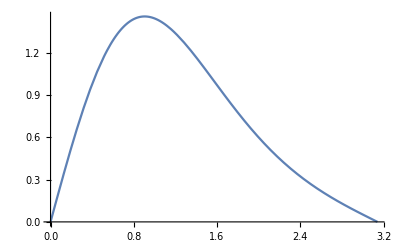

```mathematica
Plot[f[x],{x,0,Pi}]
```

```mathematica
Integrate[f[x],{x,0,Pi}] (*Integrál umíme spočítat analyticky*)
```

-1/ⅇ+ⅇ

```mathematica
a=0.;
b=Pi;
integrál=0;
m=Length[váhy];
```

```mathematica
For[i=1,i<=m,i++,
integrál=integrál+váhy[[i,2]]*(b-a)/2*f[((b-a)*váhy[[i,1]]+a+b)/2]
]
integrál-Integrate[f[x],{x,0,Pi}]
```

-0.00217422